```mathematica
s=Import["C:\\Users\\ethan\\Desktop\\Immigration\\WorldData\\modified_World_Bank.ods"]
```

```mathematica
(* Domitican Republic *)
2000-2014
im_raw = 
im={-4.04,-3.81,-3.59,-3.43,-3.22,-3.02,-2.79,-2.59,-2.4,-2.22,-2.04,-2.01,-1.98,-1.96,-1.93};
```

```mathematica
2006-2013;
```

```mathematica
pop = s[[1]][[3]][[4;;11]]
```

{1.57147,1.4377,1.40928,1.38089,1.35278,1.32462,1.29644,1.26743}

```mathematica
gdp = s[[1]][[36]][[4;;11]];
```

```mathematica
2001-2013;
```

```mathematica
unem= {15,14.5,16.5,17,17,16,15.6,15.5,14.9,14.2,13.1,14.7,15};
```

```mathematica
(* Data thats paired with the immigration vaules *)
popIm = Table[{pop[[i-6]],im[[i]]},{i,7,14}]
```

{{1.57147,-2.79},{1.4377,-2.59},{1.40928,-2.4},{1.38089,-2.22},{1.35278,-2.04},{1.32462,-2.01},{1.29644,-1.98},{1.26743,-1.96}}

```mathematica
gdpIm = Table[{gdp[[i-6]],im[[i]]},{i,7,14}]
```

{{5.6566,-2.79},{10.6712,-2.59},{8.47462,-2.4},{3.14371,-2.22},{0.935781,-2.04},{8.30215,-2.01},{2.82088,-1.98},{2.62951,-1.96}}

```mathematica
2001-2013
```

```mathematica
unemIm = Table[{unem[[i-1]],im[[i]]},{i,2,13}]
```

{{15,-3.81},{14.5,-3.59},{16.5,-3.43},{17,-3.22},{17,-3.02},{16,-2.79},{15.6,-2.59},{15.5,-2.4},{14.9,-2.22},{14.2,-2.04},{13.1,-2.01},{14.7,-1.98}}

```mathematica
(* the NonLinear functions between the factors and immigration *)
```

```mathematica
nlmGDP=NonlinearModelFit[gdpIm,c*-Log[a+b*x],{a,b,c},x]
```

FittedModel[-0.366319 Log[153.594+67.1335 x]]

```mathematica
nlmPOP =  NonlinearModelFit[popIm,-Log[a+b*x],{a,b,c},x]
```

FittedModel[-Log[-33.3292+31.2808 x]]

```mathematica
nlmUNEM= NonlinearModelFit[unemIm,-1*c*Log[a+b*x],{a,b,c},x]
```

FittedModel[-0.986393 Log[-47.8129+4.2353 x]]

```mathematica
FittedModel[-7.198678236795037 Log[23.057296288945672-18.971982106589383 x]][15]
```

-40.0716-22.6153 ⅈ

```mathematica
FittedModel[0.23092374088361556 Log[-19.992801926631046-1.093956658621401 x]]
```

FittedModel[0.230924 Log[-19.9928-1.09396 x]]

```mathematica
FittedModel[0.37733171103228236 Log[-41.89201113971086+0.18310666162215694 x]]
```

FittedModel[0.377332 Log[-41.892+0.183107 x]]

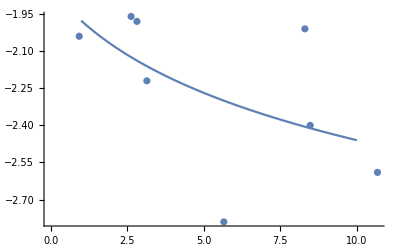

```mathematica
(* The Plots comapairing the models to the list Plots, Rememeber the 
Domain for the nlm is the factor (population , crop yeild ect) not a year *)
Show[ListPlot[gdpIm],Plot[nlmGDP[i],{i,1,10}]]
```

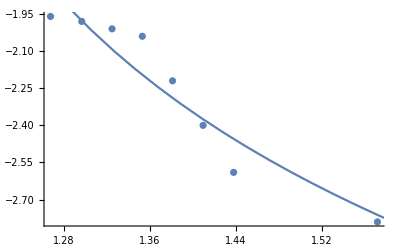

```mathematica
Show[ListPlot[popIm],Plot[nlmPOP[i],{i,1,2}]]
```

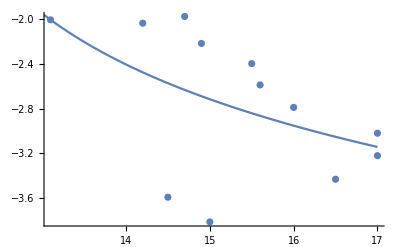

```mathematica
Show[ListPlot[unemIm],Plot[nlmUNEM[i],{i,13,17}]]
```

```mathematica
(*All combined With manipulatable factors *)
```

```mathematica
Manipulate[Mean[{nlmGDP[c1],nlmPOP[c2],nlmUNEM[c3]}],{{c1,1,"GDP Growth %"},1,10},{{c2,1.3,"Population Growth %"},1.3,3},{{c3,13,"Unemployment Rate % of workforce"},13,20}]
```

```mathematica
??Manipulate
```

RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a version of StyleBox["expr", "TI"] with controls added to allow interactive manipulation of the value of StyleBox["u", "TI"]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]], ",", StyleBox["du", "TI"]}], "}"}]}], "]"}] allows the value of StyleBox["u", "TI"] to vary between SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]] and SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]] in steps StyleBox["du", "TI"]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]]}], "}"}], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] takes the initial value of StyleBox["u", "TI"] to be SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["lbl", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] labels the controls for StyleBox["u", "TI"] with SubscriptBox[StyleBox["u", "TI"], StyleBox["lbl", "TI"]]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}]}], "]"}] allows StyleBox["u", "TI"] to take on discrete values RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] provides controls to manipulate each of the RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["u", "TI"]], "→", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], ",", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["v", "TI"]], "→", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], ",", StyleBox["…", "TR"]}], "]"}] links the controls to the specified controllers on an external device.

Attributes[Manipulate]={HoldAll,Protected,ReadProtected}
 
Options[Manipulate]={Alignment→Automatic,AppearanceElements→Automatic,AutoAction→False,AutorunSequencing→Automatic,BaselinePosition→Automatic,BaseStyle→{},Bookmarks→{},ContentSize→Automatic,ContinuousAction→Automatic,ControlAlignment→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,ControlPlacement→Automatic,ControlType→Automatic,DefaultBaseStyle→Manipulate,DefaultLabelStyle→ManipulateLabel,Deinitialization:>None,Deployed→False,Evaluator→Automatic,Frame→False,FrameLabel→None,FrameMargins→Automatic,ImageMargins→0,Initialization:>None,InterpolationOrder→Automatic,LabelStyle→{},LocalizeVariables→True,Method→{},Paneled→True,PreserveImageOptions→True,RotateLabel→False,SaveDefinitions→False,ShrinkingDelay→0,SynchronousInitialization→True,SynchronousUpdating→Automatic,TouchscreenAutoZoom→False,TouchscreenControlPlacement→Automatic,TrackedSymbols→Full,UndoTrackedVariables:>None,UnsavedVariables:>None,UntrackedVariables:>None}